```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/pedro/seagate_4tb/Dropbox/beta-Planck/alpha_ng

```mathematica
LaunchKernels[1]
```

{KernelObject[…]}

## Importing and reorganizing data

```mathematica
(*Observational data*)
```

```mathematica
nilcresults=Import["data/nilc_obs_TTEE_ab_dopp_abdopp_CorrUnbiasedVEC_lmin_200_lmax_1800.dat"]*c;
smicaresults=Import["data/smica_obs_TTEE_ab_dopp_abdopp_CorrUnbiasedVEC_lmin_200_lmax_1800.dat"]*c;
```

```mathematica
(*Simulations data*)
```

```mathematica
nilcSIMS=Import["data/nilcTTEE_with_absbias.hdf",{"Datasets","Dataset1"}];
smicaSIMS=Import["data/smicaTTEE_with_absbias.hdf",{"Datasets","Dataset1"}];
```

```mathematica
fiducialVECS=Import["data/xyz_fiducial_48_directions_vecs.dat"]*c;
dipole=Import["data/dipole_xyz_fiducial_vec.dat"][[All,1]]*c;
```

```mathematica
(*Simulations errors - PRL histogram*)
smicaTTEEabDiff=Flatten[Table[smicaSIMS[[1,dir,sim]]*c-fiducialVECS[[dir]],{dir,1,48},{sim,1,64}],1];
smicaTTEEdoppDiff=Flatten[Table[smicaSIMS[[2,dir,sim]]*c-fiducialVECS[[dir]],{dir,1,48},{sim,1,64}],1];
smicaTTEEpvDiff=Flatten[Table[smicaSIMS[[3,dir,sim]]*c-fiducialVECS[[dir]],{dir,1,48},{sim,1,64}],1];
nilcTTEEabDiff=Flatten[Table[nilcSIMS[[1,dir,sim]]*c-fiducialVECS[[dir]],{dir,1,48},{sim,1,64}],1];
nilcTTEEdoppDiff=Flatten[Table[nilcSIMS[[2,dir,sim]]*c-fiducialVECS[[dir]],{dir,1,48},{sim,1,64}],1];
nilcTTEEpvDiff=Flatten[Table[nilcSIMS[[3,dir,sim]]*c-fiducialVECS[[dir]],{dir,1,48},{sim,1,64}],1];
```

## Defining useful functions and ranges

```mathematica
UpperBound[absDist_,p_]:=Quantile[absDist,p] (*p defines the p-value of the upper bound*)
CI[absDist_,pOfRegion_]:={Quantile[absDist,(1-pOfRegion)/2],Quantile[absDist,1-(1-pOfRegion)/2]}
pσfun[pvalue_]:=FindRoot[Erf[σ/(√2)]==1-pvalue,{σ,1.01,0,7},MaxIterations->3000];(*From pvalue to σ-value*)
betafid=0.00123357;
c=299792.458;
```

## Defining alpha

```mathematica
alphasmica =(smicaresults[[2]]-dipole)/(dipole-smicaresults[[1]]);
alphanilc = (nilcresults[[2]]-dipole)/(dipole-nilcresults[[1]]);
```

## Measuring bounds and CIs

### α bootstrap distribution

```mathematica
nsims=5*10^7;
```

```mathematica
repeateddipole = Table[dipole,{n,1nsims}];
```

```mathematica
bootstrapdist1=Table[RandomInteger[{1,3072}],{n,1,nsims}];(*bootstrap based on index*)
bootstrapdist2=Table[RandomInteger[{1,3072}],{n,1,nsims}];(*bootstrap based on index*)
alphasmicadistbootstrap = (Table[smicaresults[[2]],{n,1,nsims}]+smicaTTEEdoppDiff[[bootstrapdist1]]-repeateddipole)/(repeateddipole-Table[smicaresults[[1]],{n,1,nsims}]-smicaTTEEabDiff[[bootstrapdist2]]);
```

```mathematica
bootstrapdist1=Table[RandomInteger[{1,3072}],{n,1,nsims}];(*bootstrap based on index*)
bootstrapdist2=Table[RandomInteger[{1,3072}],{n,1,nsims}];(*bootstrap based on index*)
alphanilcdistbootstrap = (Table[nilcresults[[2]],{n,1,nsims}]+nilcTTEEdoppDiff[[bootstrapdist1]]-repeateddipole)/(repeateddipole-Table[nilcresults[[1]],{n,1,nsims}]-nilcTTEEabDiff[[bootstrapdist2]]);
```

### Defining KDE distributions

```mathematica
𝒟xsmica=SmoothKernelDistribution[alphasmicadistbootstrap[[All,1]],InterpolationPoints->10000000,PerformanceGoal->"Quality"];
𝒟ysmica=SmoothKernelDistribution[alphasmicadistbootstrap[[All,2]],InterpolationPoints->10000000,PerformanceGoal->"Quality"];
𝒟zsmica=SmoothKernelDistribution[alphasmicadistbootstrap[[All,3]],InterpolationPoints->10000000,PerformanceGoal->"Quality"];
𝒟xnilc=SmoothKernelDistribution[alphanilcdistbootstrap[[All,1]],InterpolationPoints->10000000,PerformanceGoal->"Quality"];
𝒟ynilc=SmoothKernelDistribution[alphanilcdistbootstrap[[All,2]],InterpolationPoints->10000000,PerformanceGoal->"Quality"];
𝒟znilc=SmoothKernelDistribution[alphanilcdistbootstrap[[All,3]],InterpolationPoints->10000000,PerformanceGoal->"Quality"];
```

### Product of likelihoods and renormalization

```mathematica
likelihoodprodsmica[x_]:=PDF[𝒟xsmica,x]*PDF[𝒟ysmica,x]*PDF[𝒟zsmica,x]
likelihoodprodnilc[x_]:=PDF[𝒟xnilc,x]*PDF[𝒟ynilc,x]*PDF[𝒟znilc,x]
```

```mathematica
normsmica=NIntegrate[likelihoodprodsmica[x],{x,-90,90},MaxRecursion->20];
normnilc=NIntegrate[likelihoodprodnilc[x],{x,-90,90},MaxRecursion->20];
likelihoodprodrenormsmica[x_]:=likelihoodprodsmica[x]/normsmica
likelihoodprodrenormnilc[x_]:=likelihoodprodnilc[x]/normnilc
```

```mathematica
(*PDFs*)
```

```mathematica
𝒟prodSMICA=ProbabilityDistribution[likelihoodprodrenormsmica[x],{x,-Infinity,Infinity}];
𝒟prodNILC=ProbabilityDistribution[likelihoodprodrenormnilc[x],{x,-Infinity,Infinity}];
```

### Final results and plots

#### CI

```mathematica
CI[RandomVariate[𝒟prodSMICA,1000000],0.68]
CIsmica95=CI[RandomVariate[𝒟prodSMICA,1000000],0.95]
CI[RandomVariate[𝒟prodSMICA,1000000],0.999]
```

{-0.540073,2.28264}

{-2.87099,4.01278}

{-8.31804,9.22545}

```mathematica
NIntegrate[likelihoodprodrenormsmica[x],{x,-2.879992016982451,4.010105728240494}](*Checking interval probability*)
```

0.950129

```mathematica
CI[RandomVariate[𝒟prodNILC,1000000],0.68]
CInilc95=CI[RandomVariate[𝒟prodNILC,1000000],0.95]
CI[RandomVariate[𝒟prodNILC,1000000],0.999]
```

{-0.610656,1.76743}

{-2.35454,3.25783}

{-6.98259,7.83198}

```mathematica
NIntegrate[likelihoodprodrenormnilc[x],{x,-2.3578646540688935,3.2534858903712527}](*Checking interval probability*)
```

0.949687

#### α

```mathematica
alphasmicaobs=ArgMax[likelihoodprodrenormsmica[x],x] (*SMICA*)
alphanilcobs=ArgMax[likelihoodprodrenormnilc[x],x] (*NILC*)
```

1.12081

0.722346

```mathematica
CIsmica95-alphasmicaobs (*SMICA*)
```

{-3.9918,2.89196}

```mathematica
CInilc95-alphanilcobs (*NILC*)
```

{-3.07689,2.53548}

#### f_nl^local adiabatic

```mathematica
fnlSMICA=alphasmicaobs*(-2/6)(*SMICA*)
fnlNILC=alphanilcobs*(-2/6)(*NILC*)
```

-0.373605

-0.240782

```mathematica
CIfnlSMICA=Sort[CIsmica95*(-2/6)](*SMICA*)
```

{-1.33759,0.956995}

```mathematica
CIfnlNILC=Sort[CInilc95*(-2/6)](*NILC*)
```

{-1.08594,0.784848}

```mathematica
CIfnlSMICA-fnlSMICA
```

{-0.963987,1.3306}

```mathematica
CIfnlNILC-fnlNILC
```

{-0.84516,1.02563}

#### σ-value

```mathematica
pvaluefirsttailsmica=CDF[𝒟prodSMICA,0];
pvaluesecondtailsmica=(1-CDF[𝒟prodSMICA,2*ArgMax[likelihoodprodrenormsmica[x],x]]);(*Mesma distância com relação ao pico que o valor 0*)
pvaluefirsttailnilc=CDF[𝒟prodNILC,0];
pvaluesecondtailnilc=(1-CDF[𝒟prodNILC,2*ArgMax[likelihoodprodrenormnilc[x],x]]);
```

```mathematica
pσfun[pvaluefirsttailsmica+pvaluesecondtailsmica]
```

{σ→0.833262}

```mathematica
pσfun[pvaluefirsttailnilc+pvaluesecondtailnilc]
```

{σ→0.636385}

#### Plots

```mathematica
plotsmica=Plot[{PDF[𝒟prodSMICA,x],PDF[𝒟xsmica,x],PDF[𝒟ysmica,x],PDF[𝒟zsmica,x]},{x,-15,15},PlotRange->Full,Frame->True,FrameLabel->{"α^NG","","PDF - SMICA=continuous NILC=dashed",""}];
```

```mathematica
plotnilc=Plot[{PDF[𝒟prodNILC,x],PDF[𝒟xnilc,x],PDF[𝒟ynilc,x],PDF[𝒟znilc,x]},{x,-15,15},PlotRange->Full,PlotLegends->SwatchLegend[{"Total","Δ_(1, x) and β_x^(X = Ab, Dopp)","Δ_(1, y) and β_y^(X = Ab, Dopp)","Δ_(1, z) and β_z^(X = Ab, Dopp)"}],Frame->True,PlotStyle->Dashed,FrameLabel->{"α^NG","","PDF - SMICA=continuous NILC=dashed",""}];
```

```mathematica
Export["plotsmica_alpha.pdf",plotsmica]
Export["plotnilc_alpha.pdf",plotnilc]
```

plotsmica_alpha.pdf

plotnilc_alpha.pdf

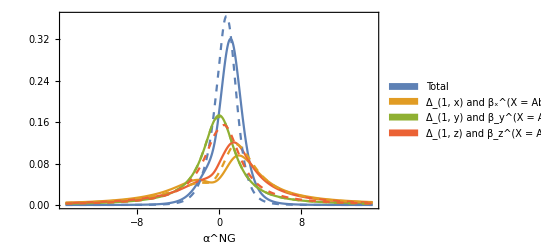

```mathematica
plotsmicaandnilc=Show[{plotsmica,plotnilc},PlotRange-> Full]
```

```mathematica
Export["plot_alpha.pdf",plotsmicaandnilc]
```

plot_alpha.pdf